# Cloud Twitter Harvester and Dashboard

This notebook shows the general workflow and code used in the Cloud Twitter Harvester and Dashboard. The code itself is not meant to be used to deploy the system, just give an idea of how it works.

To deploy the Cloud Twitter Harvester and Dashboard, please see Deployment.nb.

Before proceeding, there is one notable limit that should be mentioned. This system will only work for a period of time and is not designed to run indefinitely. This limit is due to the fact that Databins cannot grow infinitely large. Depending on the specific use case, there are three solutions to this problem.

The analysis only needs to be for a short time - This is the easiest as the system will work out of the box. Just be sure to stop the tasks once the time period is over.

The analysis is on going, but only needs to go back so far, i.e. only the past week - This can be done by creating an additional task that removes ‘expired’ data from the Databin keeping the total amount under the limit. In this case, the ‘expired’ data is lost forever, or at least the processed data is, so this should only been done if you definitely don’t need old data.

The analysis needs to go on forever - This is the hardest to handle, but can be done by creating a task that will roll the old data over into a new Databin when the active one starts to fill up. This in itself isn’t too hard, but the graphics for the dashboard will have a harder time since they need to combine data from multiple bins. One solution to that problem would be to reduce the data being rolled over by grouping in the desired way for the graphics, i.e. we don’t need a second-by-second replay of the data, but could group things by hour.

## Harvesting

Within the harvesting process, there are three major components; the reaper, the processor, and the silo.

The reaper is a cloud task that accesses Twitter and gets the raw data. It does some minor cleaning, but its main purpose is to simply get the data.

The processor is also a cloud task, but instead of accessing Twitter, it goes through the data gathered by the reaper and cleans it further, does any kind of individual analysis (i.e. sentiment analysis or identifying the geo-location), and stores the formatted data in the silo.

The silo is a Databin that stores all processed data. By storing the data in a Databin rather than a file, import speeds and queries are improved. That is, it becomes much easier to request data from certain time ranges or only specific fields rather than the dataset as a whole.

## Reaper Task

To make the task easier to modify, the code for the reaper task has been broken into three segments; a package containing general functions, a package containing the specific higher-level functions to be called by the task, and the task itself.

### TwitterReaper.wl

This package contains the general functions needed to connect to Twitter and gather data about a specific search term. It selects only the relevant fields of data, but does no further processing before saving the data to a file within the ‘Holding’ directory.

```mathematica
BeginPackage["TwitterReaper`"];

SetAuthentication;
URLRequest;
TwitterRequest;
SetProjectDirectory;
GatherTweets;

Begin["`Private`"];

$TwitterAuthenticationKey = Missing[];

(* SetAuthentication is used to import the specific tokens required to authenticate to the Twitter API. 
The object storing these tokens should be Private for security, but should be in the cloud in order for the task to be able to access them. *)
SetAuthentication[assoc_Association] := ($TwitterAuthenticationKey = SecuredAuthenticationKey[<|"Name" -> "Twitter", "ConsumerKey" -> Lookup[assoc, "ConsumerKey"], "ConsumerSecret" -> Lookup[assoc, "ConsumerSecret"], "SignatureMethod" -> {"HMAC", "SHA1"}, "OAuthVersion" -> "1.0a", "OAuthType" -> "OneLegged", "OAuthToken" -> Lookup[assoc,"OAuthToken"], "OAuthTokenSecret" -> Lookup[assoc, "OAuthTokenSecret"]|>];)
SetAuthentication[f_String] := SetAuthentication[Get[f]]
SetAuthentication[f_File] := SetAuthentication[Get[f]]
SetAuthentication[co_CloudObject] := SetAuthentication[Get[co]]

(* This is the function actually used to make the request to Twitter. It returns both the StatusCode and Body of the response in order to determine if an error has occurred. *)
URLRequest[query_, auth_] :=
	URLRead[
		HTTPRequest[
			<|
				"Scheme"->"https",
				"Domain"->"api.twitter.com",
				"Path"->"/1.1/search/tweets.json",
				"Query"->query
			|>
		], 
		{"StatusCode","Body"}, 
		Authentication -> auth
	]

(* TwitterRequest takes a term or List of parameters to be used to make the request to Twitter.
If only a term is provided, be default the count will be limited to the past 100 most recent tweets.
Additionally, the value of $TwitterAuthenticationKey (set by SetAuthentication) will be used to authenticate the request. *)
TwitterRequest[term_String] := URLRequest[{"q"->term, "result_type"->"recent", "count"->"100"}, $TwitterAuthenticationKey]
TwitterRequest[params_List] := URLRequest[params, $TwitterAuthenticationKey]

(* Defines the directory in which the harvesting system is defined. *)
SetProjectDirectory[path_] := ($workingDirectory = path;)

(* GatherTweets is used to make the correct request to Twitter plus do the initial data cleaning.
Note: the data should not be completely cleaned up here, the task should simply be gather the specific fields that you want to preserve. *)
GatherTweets[term_] := 
	Module[{paramLoc = CloudObject[URLBuild[{$workingDirectory, term<>"-params"}]],
			dataLoc, params, runTime = DateString[{"Year","Month","Day","-","Hour24","Minute","Second","-",term}],
			tweets, rawTweets, response, body, freshURL, nextParams, results},
		params = CloudGet[paramLoc];
		response = If[FailureQ[params],
				TwitterRequest[term],
				TwitterRequest[params]
			];
		If[response["StatusCode"] =!= 200,
			Return[$Failed]
		];
		body = ImportString[response["Body"], "JSON"];
		
		freshURL = Lookup[Lookup[body, "search_metadata"], "refresh_url"];
		nextParams = Append[Rule@@@URLDecode[StringSplit[StringSplit[StringTake[freshURL, 2;;], "&"], "="]], Rule["count", 100]];
		CloudPut[nextParams, paramLoc];

		rawTweets = Lookup[body, "statuses"];
		tweets = Map[processTweet, rawTweets];
		dataLoc = CloudObject[URLBuild[{$workingDirectory, "Holding", runTime}]];
		results = Map[Check[PutAppend[#, dataLoc], $Failed]&, tweets];
		If[And@@Map[FailureQ, results],
			DeleteObject[paramLoc];
			$Failed,
			dataLoc
		]
	]

(* Used to thin out the fields of data. *)
processTweet[data_] := 
	ExportString[
		MapAt[
			selectUserKeys,
			selectTweetKeys[data],
			Key["user"]
		],
		"JSON",
		"Compact"->True
	]
	
selectTweetKeys[data_] := KeySelect[data, MemberQ[$relevantTweetKeys, #]&]

$relevantTweetKeys = {
	"created_at",
	"id",
	"text",
	"source",
	"user",
	"geo",
	"coordinates",
	"place",
	"retweet_count",
	"favorite_count",
	"lang"
};

selectUserKeys[data_] := KeySelect[data, MemberQ[$relevantUserKeys, #]&]

$relevantUserKeys={"id", "screen_name", "location", "followers_count"};

End[];
EndPackage[]
```

### ReaperCode.wl

This package is defined to be the code run by the ReaperTask. It is defined within a separate package rather than the task for two reasons:
1. It makes it easier to deploy multiple ReaperTasks since the task code is much shorter.
2. It makes it easier to make changes to the ReaperTasks since the task code can now be modified without accidentally modifying the schedule for the task.

```mathematica
Block[{term = "starbucks", dir = "TwitterAnalysis"},
(* Get the general package *)
 Get[CloudObject[FileNameJoin[{dir, "TwitterReaper.wl"}]]];
 (* Setup authentication *)
 TwitterReaper`SetAuthentication[CloudObject[FileNameJoin[{dir, "AccessTokens.wl"}]]];
 (* Setup the project directory *)
 TwitterReaper`SetProjectDirectory[dir];
 (* Gather the tweets *)
 TwitterReaper`GatherTweets[term]
]
```

### ReaperTask

This is all the code that is needed to deploy the ReaperTask. A couple of things to note:
• NotificationFunction is set to None in order to prevent messages about task failures. If you wish to be notified when the task fails, you can change it to Automatic.
• The schedule for this task is set to “Hourly” but can be changed for your individual situation. The schedule should be setup such that you are making requests to Twitter frequently enough to not miss many tweets but not so frequent as to get tweets multiple times. Additionally, it should be noted that the Wolfram Public Cloud limits tasks to only run, at most, once per hour, so if you wish for more frequent reaping, you will either need to deploy multiple tasks or by using a Wolfram Enterprise Private Cloud.

```mathematica
CloudDeploy[
	ScheduledTask[
		Get["TwitterAnalysis/ReaperCode.wl"],
		"Hourly",
		NotificationFunction->None
	],
	"TwitterAnalysis/reaper.task"
]
```

## Processor Task

### TwitterProcessor.wl

This package contains the general functions needed to refine the data gathered from Twitter and upload it to the Silo Databin. It does not connect to Twitter, just reads in the data found within the specified files, tries to process the data uploading it to the Silo Databin if successful and moving the raw data to a separate folder if something fails.

```mathematica
BeginPackage["TwitterProcessor`"];

ProcessRawTwitterData;
ProcessRawTwitterFile;

Begin["`Private`"];

(* This function is used to process the raw data in different fields. *)
processTweetData[{"created_at", date_}] := {Rule["Timestamp", TimeZoneConvert[DateObject[{date, {"DayNameShort", " ", "MonthNameShort", " ", "Day", " ", "Hour24", ":", "Minute", ":", "Second", " +0000 ", "Year"}}, TimeZone -> 0]]]}
processTweetData[{"id", id_}] := {Rule["ID", id]}
processTweetData[{"text", tweet_}] := {Rule["Tweet", ToString[tweet, CharacterEncoding->"ASCII"]], Rule["Sentiment", Replace[Classify["Sentiment"][tweet], {"Positive" -> 1, "Negative" -> -1, _ -> 0}]]}
processTweetData[{"source", sourceLink_}] := {Rule["Source", sourceName[sourceLink]]}
processTweetData[{"user", userData_}] := processUserData[userData]
processTweetData[{"geo", Null}] := {}
processTweetData[{"geo", geo_}] := {Rule["geo", formatLocation[Lookup[geo, "coordinates"]]]}
processTweetData[{"coordinates", Null}] := {}
processTweetData[{"coordinates", coor_}] := {Rule["coordinates", formatLocation[Reverse[Lookup[coor, "coordinates"]]]]}
processTweetData[{"place", Null}] := {}
processTweetData[{"place", place_}] := {Rule["place", With[{loc=Check[Interpreter["Location"][Lookup[place, "full_name"]], Missing[]]}, If[FailureQ[loc], Missing[], loc]]]}
processTweetData[{"retweet_count", count_}] := {Rule["Retweets", count]}
processTweetData[{"favorite_count", count_}] := {Rule["Favorites", count]}
processTweetData[{"lang", lang_}] := {Rule["Language", With[{l = Check[Interpreter["Language"][lang], lang]}, If[FailureQ[l], lang, l]]]}

formatLocation[loc_] := Quiet[Check[GeoPosition[loc], Missing[]]]

processUserData[data_] := {Rule["User", <|"UserID" -> Lookup[data, "id"], "ScreenName" -> Lookup[data, "screen_name"], "Location" -> With[{loc = Quiet[Check[Interpreter["Location"][Lookup[data, "location"]], Missing[]]]}, If[FailureQ[loc], Missing[], loc]], "Followers" -> Lookup[data, "followers_count"]|>]}

sourceName[name_] := Replace[StringCases[name, {">Twitter for " ~~ Shortest[source__] ~~ "<" :> source}], {{value_} :> value, {values__} :> First[values], {} :> None}]

calculateLocation[data_] :=
 Module[{specific = Lookup[data, {"geo", "coordinates", "place"}]},
 Join[
 KeyDrop[data, {"geo", "coordinates", "place"}],
 <|"Location" -> 
 If[And @@ Map[MissingQ, specific], 
 Lookup[Lookup[data, "User"], "Location"],
 Last[DeleteCases[specific, _Missing|_Failure]]
 ]
 |>
 ]
 ]

(* This function takes all of the tweets and processes them individually.
On an EPC with parallel evaluations enabled, this step could be improved. *)
ProcessRawTwitterData[data_] := Map[calculateLocation[Association[Flatten[Map[processTweetData, List@@@#]]]]&, data]

(* This function takes the file to be processed, the Databin to be uploaded to, and the working directory of the system.
If the data is successfully processed and uploaded to the Databin, the raw file is moved to "Processed".
If any failure occurs, the raw file is moved to "Quarantine" to prevent it from be processed again by the task, but saved for a user to manually inspect the data for errors. *)
ProcessRawTwitterFile[file_, bin_, cDir_] :=
Module[{raw = Map[ImportString[#,"JSON"]&, ReadList[file]], data, qFile, copied},
data = ProcessRawTwitterData[raw];
Check[
DatabinUpload[bin, data],
qFile = CopyFile[CloudObject[file], CloudObject[URLBuild[{cDir, "Quarantine",FileNameTake[file]}]]];
If[!FailureQ[qFile] && FileExistsQ[qFile], DeleteObject[CloudObject[file]]];
Return[uploadFailure[file, qFile]],
Databin::apierr
];
copied = CopyFile[CloudObject[file], CloudObject[URLBuild[{cDir, "Processed", FileNameTake[file]}]]];
If[!FailureQ[copied] && FileExistsQ[copied], DeleteObject[CloudObject[file]]];
uploadSuccess[file, bin]
]

uploadSuccess[file_, bin_] := Success["DataUploaded", <|"MessageTemplate" :> "Data from `file` uploaded to `bin`", "MessageParameters" -> <|"file" -> file, "bin" -> bin["ShortID"]|>|>]

uploadFailure[file_, qFile_] := Failure["DataUploadFailure", <|"MessageTemplate" :> "Data from `file` failed to bo uploaded", "MessageParameters" -> <|"file" -> file|>, "Location" -> qFile|>]

End[];
EndPackage[]
```

### ProcessorCode.wl

This package is defined to be the code run by the ProcessorTask. It is defined within a separate package rather than the task for two reasons:
1. It makes it easier to deploy multiple ProcessorTasks since the task code is much shorter.
2. It makes it easier to make changes to the ProcessorTasks since the task code can now be modified without accidentally modifying the schedule for the task.

```mathematica
Block[{term = "starbucks", dir = "TwitterAnalysis", bin = Databin["Bin ID"]},
 Get[CloudObject[FileNameJoin[{dir, "TwitterProcessor.wl"}]]];
 Do[
  Print[file];
  TwitterProcessor`ProcessRawTwitterFile[file, bin, dir],
  {file, FileNames["*-"<>term, URLBuild[{dir, "Holding"}]]}
 ];
 "Done"
]
```

### ProcessorTask

This is all the code that is needed to deploy the ProcessorTask. A couple of things to note:
• NotificationFunction is set to None in order to prevent messages about task failures. If you wish to be notified when the task fails, you can change it to Automatic.
• The schedule for this task is set to “Hourly” but can be changed for your individual situation. The schedule should be setup such that you are able to process all of the data gathered by the ReaperTask(s). If you have more than 2 reapers, you will likely need more processors. If you notice that you have a backlog of unprocessed data, you can manually trigger the ProcessorTask in order to catch up. This can be useful if part of the system goes down for maintenance.

```mathematica
CloudDeploy[
	ScheduledTask[
		Get[CloudObject["TwitterAnalysis/ProcessCode.wl"]],
		"Hourly",
		NotificationFunction->None
	],
	"TwitterAnalysis/process.task"
]
```

## Silo Databin

The Silo Databin is probably the easiest part of the system since it requires the least about of work to create. Once the bin has been created, make sure to include the correct DatabinID in ProcessorCode.wl and for use in the Dashboard.

```mathematica
CreateDatabin[<|"Name"->"TwitterSilo"|>]
```

## Dashboard

Within the dashboard, there are two components; the individual charts/graphs/maps to be displayed and the notebook that displays all of the results.

The graphics listed below are all basic examples, but more can easily be created and added to the notebook. The basic deployment for these graphics is as an AutoRefreshed, this is in order to refresh the data being displayed without having to constantly regenerate images whenever someone wants to view them.

The dashboard notebook simply gets the latest copy of all the graphics and displays them. The layout can be changed and an HTML page can be substituted for the notebook, but this gets the idea across.

## Graphics

Each of the following subsections (with the exception of the first) is used to generate a graphic for the dashboard. They include the code for generating the graphic itself as well as the code needed to deploy the AutoRefreshed object.

### Style Utilities

This subsection defines a color pallette to be used by the graphics. This allows for a more unique feel for the dashboard since the colors can be setup for whatever topic is being analyzed.

```mathematica
Colors[] = {RGBColor[0., 0.396078431372549, 0.23137254901960785], RGBColor[1., 1., 1.], RGBColor[0.7372549019607844, 0.6235294117647059, 0.5019607843137255], RGBColor[0.26666666666666666, 0.17647058823529413, 0.09411764705882353], RGBColor[0.1843137254901961, 0.25098039215686274, 0.30980392156862746], RGBColor[0.4235294117647059, 0.42745098039215684, 0.4392156862745098], RGBColor[0.24313725490196078, 0.24313725490196078, 0.24705882352941178], RGBColor[0.13333333333333333, 0.12156862745098039, 0.12549019607843137]};
BackgroundColor[] = BackgroundColor[1] = RGBColor[0.7372549019607844, 0.6235294117647059, 0.5019607843137255];
BackgroundColor[2] = RGBColor[0.1843137254901961, 0.25098039215686274, 0.30980392156862746];
TextColor[] = TextColor[1] = RGBColor[0.26666666666666666, 0.17647058823529413, 0.09411764705882353];
TextColor[2] = RGBColor[0.13333333333333333, 0.12156862745098039, 0.12549019607843137]
TextColor[-1] = RGBColor[1., 1., 1.];
DataColor[] = DataColor[1] = RGBColor[0., 0.396078431372549, 0.23137254901960785];
DataColor[2] = RGBColor[0.4235294117647059, 0.42745098039215684, 0.4392156862745098];
DataColor[3] = RGBColor[0.26666666666666666, 0.17647058823529413, 0.09411764705882353];
```

### SentimentHistogram

#### SentimentHistogram.wl

```mathematica
Module[{max, min, full, bin=Databin["Bin ID"], data},
	data=Dataset[bin];
	Column[{
		GeoHistogram[
			Association@@Map[
				Rule[Lookup[#, "Location"], Lookup[#, "Sentiment"] * Max[Lookup[Lookup[#, "User"], "Followers"], 1]*Max[Lookup[#, "Retweets"], 1]] &,
				Normal[data[Select[And[!MissingQ[#Location], #Language === Entity["Language","English"]] &]][All, {"Location", "Sentiment", "User", "Retweets"}]]
			],
			{"Hexagon", 100},
			Function[{bins, counts},
				max = Max[counts];
				min = Min[counts];
				full = Max[Abs[{max, min}]];
				counts
			],
			ColorFunction -> Function[{i}, With[{x = (max - min)*i + min}, If[x == 0, DataColor[2], Blend[{DataColor[1], DataColor[3]}, 1 - (x + full)/(2 * full)]]]],
			GeoBackground -> GeoStyling[{"CountryBorders", "Land" -> BackgroundColor[1], "Ocean" -> BackgroundColor[2], "Border" -> Directive[TextColor[1], Dotted, Thin]}],
			ImageSize -> Full,
			PlotStyle -> Directive[EdgeForm[Directive[TextColor[1], Thickness[0.000075]]], Opacity[0.35]]
		],
		Graphics[{
			Table[{
				Blend[{DataColor[1], DataColor[3]}, 1 - i],
				Rectangle[{i, 0}, {i + 0.05, 0.05}]},
				{i, 0, 1, 0.05}
			],
			TextColor[-1],
			Text[Style["-", 24], {0.05, 0.025}, {0, 0}, Background -> None],
			Text[Style["+", 24], {1.025, 0.025}, {0, 0}, Background -> None]},
			ImageSize -> Full,
			PlotRange -> {{0, 1.05}, {0, 0.05}},
			PlotRangePadding -> None
		]},
		Spacings->0
	]
]
```

#### SentimentHistogram

```mathematica
CloudDeploy[
	AutoRefreshed[
		Get[CloudObject["TwitterAnalysis/SentimentHistogram.wl"]],
		"Hourly",
		"PNG"
	],
	"TwitterAnalysis/SentimentHistogram"
]
```

#### Example Output

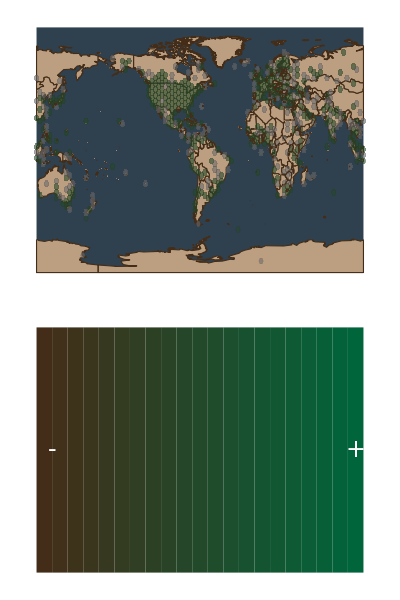

### SentimentListPlot

#### SentimentListPlot.wl

```mathematica
Module[{bin =Databin["Bin ID", All, "Sentiment"], data, quantiles},
	data = TimeSeries[
		List@@@Normal[
			Map[
				N[Total[#]]&,
				GroupBy[
					Lookup[TimeSeries[bin], "Sentiment"]["Path"],
					(DateValue[First[#], {"Year", "Month", "Day", "Hour24"}] &) -> Last
				]
			]
		]
	];
	quantiles =With[{max = Floor[Max[data], 10]}, Map[Round[max * #]&, {.2, .4, .6, .8}]];
	Framed[
		DateListPlot[{data, MovingAverage[data, 6]},
			Background -> BackgroundColor[],
			FrameStyle -> TextColor[],
			FrameTicks->{Automatic, quantiles},
			GridLines->{None, quantiles},
			GridLinesStyle->Directive[Dashed, TextColor[], Thin],
			ImageSize->Full,
			Joined->{False, True},
			PlotRange->{Automatic, {0, Automatic}},
			PlotRangePadding->{Automatic, None},
			PlotStyle->{Directive[Thickness[0.0005], DataColor[2]], DataColor[1]},
			PlotTheme->{"Wide", "Business"}
		],
		Background -> BackgroundColor[],
		FrameMargins -> {{15, 5}, {5, 15}},
		FrameStyle -> None
	]
]
```

#### SentimentListPlot

```mathematica
CloudDeploy[
	AutoRefreshed[
		Get[CloudObject["TwitterAnalysis/SentimentListPlot.wl"]],
		"Hourly",
		"PNG"
	],
	"TwitterAnalysis/SentimentListPlot"
]
```

#### Example Output

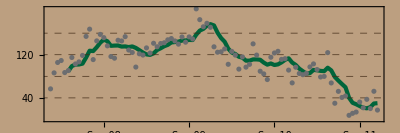

### PieCharts

#### PieCharts.wl

```mathematica
Module[{bin = Databin["Bin ID", All, {"Source","Language"}], data},
	data = Dataset[bin];
	GraphicsRow[{
		With[{sources = Normal[Counts[data[All, "Source"]]]},
			PieChart[
				Values[sources],
				Background -> None,
				ChartLegends -> Placed[ReplaceAll[Keys[sources], {None -> "Browser"}], Left],
				ChartStyle -> Colors[],
				ImageSize -> Scaled[0.48],
				SectorOrigin -> {Automatic, 1}
			]
		],
		With[{language = KeyMap[#["Name"]&, Take[KeySelect[Sort[Normal[Counts[data[All, "Language"]]], Greater], Head[#] === Entity&], UpTo[Length[colors]]]]},
			PieChart[
				Values[language],
				Background -> None,
				ChartLegends -> Placed[Keys[language], Right],
				ChartStyle -> Colors[],
				ImageSize -> Scaled[0.48],
				SectorOrigin -> {Automatic, 1}
			]
		]},
		Alignment -> Center,
		Background -> BackgroundColor[],
		ImageSize -> Full
	]
]
```

#### PieCharts

```mathematica
CloudDeploy[
	AutoRefreshed[
		Get[CloudObject["TwitterAnalysis/PieCharts.wl"]],
		"Hourly",
		"PNG"
	],
	"TwitterAnalysis/PieCharts"
]
```

#### Example Output

-Graphics-

## Dashboard Notebook

The notebook displaying all the graphics is regenerated with each visit in order to ensure that the graphics displayed are as recent as possible. If that is not necessary, the CachePersistence option can be used to defined how long the cache should live for.

```mathematica
CloudDeploy[Delayed[
	Notebook[{
		Cell["Starbucks Twitter Analysis", "Chapter", FontColor -> TextColor[]],
		Cell[BoxData[ToBoxes[
			ImageCrop[
				ImportString[
					URLRead[CloudObject["TwitterAnalysis/SentimentHistogram"], "Body"],
					"PNG"
				]
			]]], "Output"],
		Cell[BoxData[ToBoxes[
			ImageCrop[
				ImportString[
					URLRead[CloudObject["TwitterAnalysis/SentimentListPlot"], "Body"],
					"PNG"
				]
			]]], "Output"],
		Cell[BoxData[ToBoxes[
			ImageCrop[
				ImportString[
					URLRead[CloudObject["TwitterAnalysis/PieCharts"], "Body"],
					"PNG"
				]
			]]], "Output"]
		},
		Background -> BackgroundColor[],
		FontFamily -> "Roboto",
		ShowCellBracket -> False,
		TextAlignment -> Center
	]],
	"TwitterAnalysis/Dashboard",
	Permissions->"Public"
]
```